## Atomic to Physical Unit Conversions

```mathematica
(* 1 GHz below ZFIP in AU *)
enAU=Quantity[4.35974417*10^-18,"Joules"];
enAU1GHz=UnitConvert[Quantity["PlanckConstant"]*Quantity[1,"Gigahertz"]/enAU];
Print["1 GHz Photon Energy = ",enAU1GHz, " A.U."]

(* 1 ns in AU *)
tAU=Quantity[2.418884326505*10^-17,"Seconds"];
tAU1ns=UnitConvert[Quantity[1,"nanosecond"]/tAU];
Print["1 ns = ",tAU1ns, " A.U."]

(* 1 mV/cm in AU *)
fAU=Quantity[5.14220652*10^11,"Volts"/"Meters"];
fAU1mVcm=UnitConvert[Quantity[1,"Millivolts"/"Centimeters"]/fAU];
Print["1 mV/cm = ",fAU1mVcm," A.U."]
```

1 GHz Photon Energy = 1.51983×10^-7 A.U.

1 ns = 4.13414×10^7 A.U.

1 mV/cm = 1.94469×10^-13 A.U.

## Inner Turning Point Integral

```mathematica
Clear[f,W,zi,zf,z]
f=0*fAU1mVcm;
W=0*enAU1GHz;
zi=0;
zf=6;
Integrate[1/(2*(W+1/z+f*z))^(1/2),{z,zi,zf}]
```

4 √3

```mathematica
4*√3/tAU1ns
```

1.67585×10^-7

## Scratch

```mathematica
Clear[f,W,z,soln,solp]
cond={W->-100*enAU1GHz,f->10*fAU1mVcm};
(* soln=Solve[0==f*z^2+W*z-1,z]; *)
soln=Solve[W==1/z-f*z,z];
(* solp=Solve[0==f*z^2+W*z+1,z]; *)
solp=Solve[W==-1/z-f*z,z];
Print["z < 0 \t",soln]
Print["z < 0 \t",soln/.cond]
Print["z > 0 \t",solp]
Print["z > 0 \t",solp/.cond]
```

z < 0 	{{z→(-W-√(4 f+W^2))/(2 f)},{z→(-W+√(4 f+W^2))/(2 f)}}

z < 0 	{{z→-65252.},{z→7.88053×10^6}}

z > 0 	{{z→(-W-√(-4 f+W^2))/(2 f)},{z→(-W+√(-4 f+W^2))/(2 f)}}

z > 0 	{{z→66360.3},{z→7.74892×10^6}}

```mathematica
Clear[f,W,z]
W=-100*enAU1GHz;
f=10*fAU1mVcm;
(-W-√(4*f+W^2))/(2*f)
```

-65252.

```mathematica
Clear[f,W,z]
W=-100*enAU1GHz;
f=10*fAU1mVcm;
NSolve[0==W+1/z-f*z,z]
NSolve[0==W-1/z-f*z,z]
```

{{z→-7.88053×10^6},{z→65252.}}

{{z→-7.74892×10^6},{z→-66360.3}}

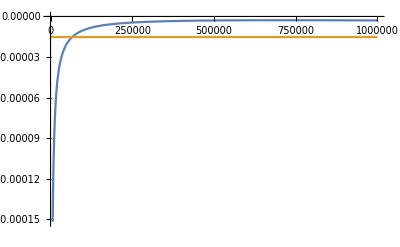

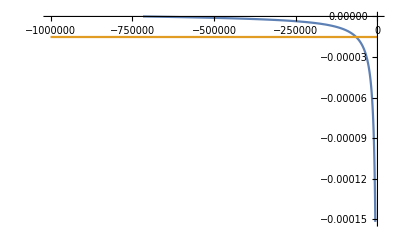

```mathematica
Clear[f,W,z]
W=-100*enAU1GHz;
f=10*fAU1mVcm;
Plot[{-1/z-f*z,W},{z,0,1000000},PlotRange->{All,{10W,0}}]
Plot[{1/z-f*z,W},{z,-1000000,0},PlotRange->{All,{10W,0}}]
```